```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/fcucchietti/Code/MathMPS

Load the library

```mathematica
<<MPS.m
```

MPS manipulation from Mathematica.
MPS Manipulation and creation:
	MPSProductState
	MPSExpandBond
	MPSNormalize
	MPSCanonize
Reading and saving to disk:
	MPSRead
	MPSSave
Expectation values:
	MPSExpectation
	MPSCorrelation
Algorithms:
	MPSApproximate
	MPSMinimizeEnergy
Hamiltonian Creation:
	MPSInitHamiltonian
	MPSHamiltonianAdd

Also available are TEBD algorithms:

Creation and disk interaction:
	TEBDProductState
	TEBDRead
	TEBDSave
Real and imaginary time evolution:
	TEBDEvolve
Expectation values:
	TEBDExpectation
	TEBDCorrelation
	TEBDentropy
	TEBDentropyList
Hamiltonians and evolution operators:
	TEBDInitHamiltonian
	TEBDHamiltonianAdd
	TEBDEvolutionFromHamiltonian
	TEBDInitEvolution
	TEBDEvolutionAddGate

Set some simulation parameters

```mathematica
bond=8; (* This will be the Bond Dimension *)
length=10; (* Length of the chain *)
intrange=1; (* Interaction range, 1 is nearest neighbor *)
μField = 0.10; (* Magnetic field *)
JCoupling=-1.0; (* Spin-spin coupling *)
```

We start by creating a random MPS.

```mathematica
mymps=MPSProductState[length,Bond->bond];
```

Normalization typically is optional, but it's a good habit

```mathematica
MPSNormalize[mymps];
```

The MPS is a nasty collection of matrices

```mathematica
mymps[[1]]//Normal
```

{{{0.248318-0.208715 ⅈ,-0.288056-0.272326 ⅈ,0.141639+0.237939 ⅈ,0.0319991-0.274733 ⅈ,0.170179+0.256107 ⅈ,-0.132218-0.144471 ⅈ,0.151968+0.263916 ⅈ,0.109178+0.331435 ⅈ}},{{0.110975-0.219034 ⅈ,0.0620832+0.0672532 ⅈ,0.294924+0.0431072 ⅈ,-0.163268+0.249712 ⅈ,-0.193414+0.183179 ⅈ,0.354245-0.0408893 ⅈ,-0.162316+0.215459 ⅈ,-0.172972-0.117588 ⅈ}}}

Now we need to create the Hamiltonian. For readability we define the axes names

```mathematica
Xaxis=1; Yaxis=2;Zaxis=3;
MyHamiltonian=MPSInitHamiltonian[length];
Do[
(* Add field terms *)
If[n==m,MPSHamiltonianAdd[MyHamiltonian,Xaxis,μField,n]];
(* Add nearest neighborg interaction *)
If[n==m+1,MPSHamiltonianAdd[MyHamiltonian,Zaxis,JCoupling,n,m]];,
{n,1,length},{m,1,length}]
```

Finally compute the ground state -- MPSMinimizeEnergy returns the energy of the state

```mathematica
(MPSenergy=MPSMinimizeEnergy[mymps,MyHamiltonian,Verbose->False,Tolerance->10^(-7),Sweeps->6])
```

-2.28009

The state has changed.

```mathematica
mymps[[1]]//Normal
```

{{{-0.117036-0.53483 ⅈ,0.0956626+0.437156 ⅈ}},{{0.11704+0.534845 ⅈ,0.0956598+0.437144 ⅈ}}}

Now improve precision by making a larger bond MPS. You can ask for help on specific commands like in Mathematica

```mathematica
?MPSExpandBond
```

MPSExpandBond[mps,newχ] expands the bond dimension χ of mps to newχ. Returns the expanded mps as a new variable

```mathematica
MPSExpandBond[mymps,15];
```

Grow χ to 15

```mathematica
Newenergy=MPSMinimizeEnergy[mymps,MyHamiltonian,Verbose->False,Tolerance->10^(-5),Sweeps->5]
```

-2.28009

Now measure something

```mathematica
?MPSExpectation
```

MPSExpectation[mps,operator,site]
MPSExpectation[mps,operator,site1,site2]
MPSExpectation[mps,operator1,site1,operator2,site2]

Computes the expectation value of one or two Hermitian operators acting on one or two sites

Let us define some operators to make it clean

```mathematica
X={{0.0,1.0},{1.0,0.0}};
Y={{0.0,-I 1.0},{I 1.0,0.0}};
Z={{1.0,0.0},{0.0,-1.0}};
Id={{1.0,0.0},{0.0,1.0}};
```

```mathematica
MPSExpectation[mymps,X,5]
```

-0.100508

A correlation can be directly plotted

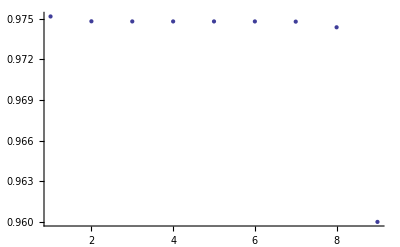

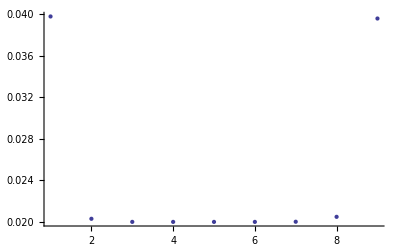

```mathematica
ListPlot[MPSCorrelation[mymps,Z,1,Z,10]]
ListPlot[MPSCorrelation[mymps,X,1,X,10]]
```

## TEBD Example

We will use the same parameters as above

```mathematica
bond=8; (* This will be the Bond Dimension *)
length=10; (* Length of the chain *)
intrange=1; (* Interaction range, 1 is nearest neighbor *)
μField = 0.1; (* Magnetic field *)
JCoupling=-1.0; (* Spin-spin coupling *)
```

```mathematica
?TEBDProductState
```

TEBDProductState[numSites,Options]
Creates a TEBD representation state. 
Options:
	Spin→integer (Default is 2)
	BondDimension→integer   (default is 20)
	Type→{type,list}     (Creates several types of TEBDs: type="Random" , "Identity", or "Specified".
						If Specified is chosen, then list must be a Table of dimensions {numSites,2}, containing in each element a pair {probAmplitude,phase}

```mathematica
mytebd=TEBDProductState[10,BondDimension->10];
```

To create the Hamiltonian we must keep in mind that the order in which the operators are added imposes the sequence in which they are implemented later in the evolution operator. In principle we can also create an evolution operator directly, which gives us even more control since we can do periodic boundary conditions or long range interactions. The control is primitive but powerful, however in the future I expect to come up with some algorithm that finds some optimal evolution operator automatically.

For now, let us see how we can make the evolution operator with imaginary time of the same system but with periodic boundary conditions. We have to first initialize

```mathematica
U=TEBDInitEvolution[];
```

```mathematica
δt=-I 0.01;
SpinZZ=(1./4)KroneckerProduct[Z,Z];
SpinX=X/2.;
```

We will do a Trotter-Suzuki evolution of second order. For this, we first add evolution gates to the odd bonds for a time δt/2

```mathematica
Do[
TEBDEvolutionAddGate[U,MatrixExp[-I δt JCoupling SpinZZ/2],i,i+1],
{i,1,9,2}]
```

Now the even bonds

```mathematica
Do[
TEBDEvolutionAddGate[U,MatrixExp[-I δt JCoupling SpinZZ/2],i,i+1],
{i,2,8,2}]
```

Now we add the field terms to all the sites

```mathematica
Do[
TEBDEvolutionAddGate[U,MatrixExp[-I δt μField SpinX],i],
{i,1,10,1}]
```

To complete the second order Trotter-Suzuki, we need to add the same gates but in transposed order

```mathematica
Do[
TEBDEvolutionAddGate[U,MatrixExp[-I δt JCoupling SpinZZ/2],i,i+1],
{i,2,8,2}];
Do[
TEBDEvolutionAddGate[U,MatrixExp[-I δt JCoupling SpinZZ/2],i,i+1],
{i,1,9,2}];
```

We have a total of

```mathematica
Length[U]
```

28

gates per evolution step (the swaps add a lot of work).

Let us see if it works by applying this 1000 times...

```mathematica
error=TEBDEvolve[mytebd,U,2000,Verbose->True]
```

-90.324

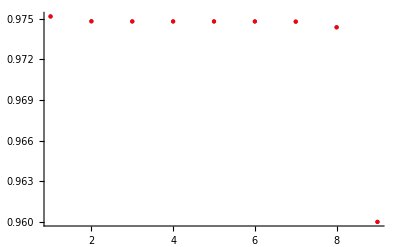

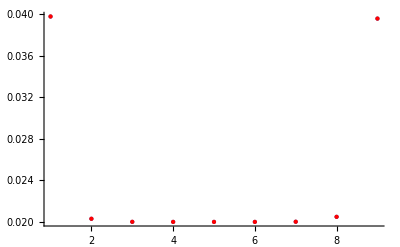

```mathematica
Show[ListPlot[MPSCorrelation[mymps,Z,1,Z,10]],ListPlot[TEBDCorrelation[mytebd,Z,1,Z,10],PlotStyle->Red]]
Show[ListPlot[MPSCorrelation[mymps,X,1,X,10]],ListPlot[TEBDCorrelation[mytebd,X,1,X,10],PlotStyle->Red]]
```

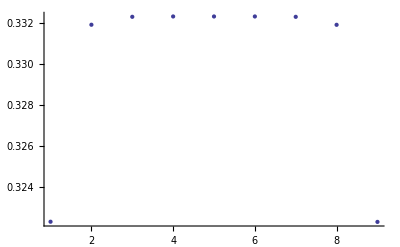

```mathematica
ListPlot[TEBDEntropyList[mytebd]]
```

Overlaps can be calculated by the expectation value of Identity...maybe I will improve this later

```mathematica
TEBDExpectation[mytebd,Id,1]
```

1.

```mathematica
IsingEnergy[TEBD_]:=JCoupling Sum[TEBDExpectation[TEBD,Z/2,i,Z/2,i+1],{i,1,9}]+μField Sum[TEBDExpectation[TEBD,X/2,i],{i,1,10}]
```

```mathematica
IsingEnergy[mytebd]
```

-2.28009

HOW TO DO A PERIODIC BOUNDARY CONDITION SYSTEM

The end-to-end coupling needs to be done by swapping the first and last spins until they are next to each other. For this, we add a long range interaction

```mathematica
TEBDEvolutionAddGate[U,MatrixExp[-I δt JCoupling SpinZZ/2],1,10];
```

In the appropriate places (before the field terms, after all the other interactions).
The library will take care of all the required Swaps needed to realize this interaction.